# Visibility of different interference measures

## Definitions

Here we define all the functions needed for our analysis

### Default Plot style

```mathematica
SetOptions[Plot, BaseStyle -> {FontFamily -> "Times", FontSize -> 30},
   Frame -> True, ImageSize -> 72*{8*GoldenRatio, 8}, 
  AspectRatio -> 1/GoldenRatio, LabelStyle -> Directive[Bold, FontSize -> 30,FontFamily -> "Times",FontColor->Black], 
  GridLines -> Automatic,PlotStyle->{AbsoluteThickness[3.5]}];
```

### Useful functions

```mathematica
(*Inverse mode occupation to obtain λ*)
InvModOcc[n_]:=Sqrt[n/(1+n)] 
(*Calculates the visibility*)
Vis[a_,b_]:=If[a==0&&b==0,0,1-Min[{Abs[a],Abs[b]}]/Max[{Abs[a],Abs[b]}]];
```

### Probabilities of different states

```mathematica
(*Coefficient of the wavefunction after the beam splitter in the Fock basis, Note that this is the most important defintion as all others rely upon it*)
CF[Y_,X_,W_,Z_,λ_,ϕ1_,ϕ2_]:=(1-λ^2)*(λ/2)^(W+Y)*Sqrt[Factorial[Y]*Factorial[X]*Factorial[W]*Factorial[Z]]*Sum[1/(Factorial[m]*Factorial[W+Y-m])*Sum[Sum[I^(W+Z+2*m-2*k-2*n)*Exp[I*ϕ1*(W-m)+I*ϕ2*(Z-m)]*Binomial[X+Z-m,W-k]*Binomial[m,k]*Binomial[W+Y-m,Z-n]*Binomial[m,n],{n,Max[0,m-X],Min[m,Z]}],{k,Max[0,m-Y],Min[m,W]}],{m,0,W+Y}]
Cf[Y_,X_,W_,Z_,λ_,ϕ_]:=If[X+Z≠Y+W,0,CF[Y,X,W,Z,λ,ϕ,ϕ]]
(*Probability of a given (complete) four particle state, equal to cc^**)
Pst[Y_,W_,X_,λ_,ϕ_]:=If[X>Y+W,0,Abs[Cf[Y,X,W,Y+W-X,λ,ϕ]]^2]
Pstate[Y_,W_,X_,λ_,ϕ1_,ϕ2_]:=If[X>Y+W,0,Abs[CF[Y,X,W,Y+W-X,λ,ϕ1,ϕ2]]^2]
(*Probability of a two particle state, tracing over the othe half*)
Pb[Y_,W_,λ_,ϕ_]:=Sum[Abs[Cf[Y,X,W,Y+W-X,λ,ϕ]]^2,{X,0,Y+W}]
(*Probability of seeing a given total number of particles*)
Pnum[Num_,λ_,ϕ_]:=Sum[Pb[Num-x,x,λ,ϕ],{x,0,Num}]
(*Probability of seeing a noncoincidence state*)
Pnc[λ_,ϕ_]:=Pb[0,0,λ,ϕ]+Sum[Pb[i,0,λ,ϕ]+Pb[0,i,λ,ϕ],{i,1,7}]
(*Probability of seeing a noncoincidence state for the four port case*)
Pnc4[λ_,ϕ_]:=Pst[0,0,0,λ,ϕ]+Sum[Pst[0,Y,Y,λ,ϕ]+Pst[Y,0,Y,λ,ϕ]+Pst[0,Y,0,λ,ϕ]+Pst[Y,0,0,λ,ϕ],{Y,1,4}]+Sum[Sum[Pst[Y,W,0,λ,ϕ]+Pst[Y,W,Y+W,λ,ϕ]+Pst[Y+W,0,Y,λ,ϕ]+Pst[0,Y+W,Y,λ,ϕ],{W,1,4}],{Y,1,4}]
```

### Expectation functions for g2's

```mathematica
(*Expectation value of some function f*)
Ex[f_,λ_,ϕ_,T_]:=Sum[Sum[Sum[Pst[Y,W,X,λ,ϕ]*f,{X,0,Y+W}],{Y,0,T}],{W,0,T}]
(*general colinear g2*)
g2CL[f_,λ_,ϕ_,T_]:=Ex[f*(f-1),λ,ϕ,T]/(Ex[f,λ,ϕ,T]*Ex[f,λ,ϕ,T])
(*general independant g2*)
g2[g_,f_,λ_,ϕ_,T_]:=Ex[f*g,λ,ϕ,T]/(Ex[f,λ,ϕ,T]*Ex[g,λ,ϕ,T])
(*general independant g3*)
g3[h_,g_,f_,λ_,ϕ_,T_]:=Ex[f*g*h,λ,ϕ,T]/(Ex[h,λ,ϕ,T]*Ex[f,λ,ϕ,T]*Ex[g,λ,ϕ,T])
(*independant g4*)
g4[e_,h_,g_,f_,λ_,ϕ_,T_]:=Ex[e*f*g*h,λ,ϕ,T]/(Ex[h,λ,ϕ,T]*Ex[f,λ,ϕ,T]*Ex[g,λ,ϕ,T]*Ex[e,λ,ϕ,T])
(*the mains g2 functions*)
g2cpcm[λ_,ϕ_,T_]:=g2[X,Y,λ,ϕ,T]
g2dpdm[λ_,ϕ_,T_]:=g2[W,Y+W-X,λ,ϕ,T]
g2cmdm[λ_,ϕ_,T_]:=g2[W,Y,λ,ϕ,T]
g2cpdp[λ_,ϕ_,T_]:=g2[X,Y+W-X,λ,ϕ,T]
g2cpdm[λ_,ϕ_,T_]:=g2[X,W,λ,ϕ,T]
g2dpcm[λ_,ϕ_,T_]:=g2[Y,Y+W-X,λ,ϕ,T]
g2cpcp[λ_,ϕ_,T_]:=g2CL[X,λ,ϕ,T]
g2cmcm[λ_,ϕ_,T_]:=g2CL[Y,λ,ϕ,T]
g2dmdm[λ_,ϕ_,T_]:=g2CL[W,λ,ϕ,T]
g2dpdp[λ_,ϕ_,T_]:=g2CL[Y+W-X,λ,ϕ,T]
(*g3*)
g3cpcmdm[λ_,ϕ_,T_]:=g3[X,Y,W,λ,ϕ,T]
g3cpdpdm[λ_,ϕ_,T_]:=g3[X,Y+W-X,W,λ,ϕ,T]
(*g4*)
g4cpdpcmdm[λ_,ϕ_,T_]:=g4[X,Y,W,Y+W-X,λ,ϕ,T]
(**)
Ecpdpcmdm[λ_,ϕ_,T_]:=Sum[Sum[Sum[Pst[Y,W,X,λ,ϕ]*Y*X*W*(Y+W-X),{X,0,Y+W}],{W,0,T}],{Y,0,T}]
Ecpcm2[λ_,ϕ_,T_]:=Sum[Sum[Sum[Pst[Y,W,X,λ,ϕ]*(X*Y)^2,{W,Max[X-Y,0],Max[X-Y,0]+T}],{Y,0,T}],{X,0,T}]
Edpdm2[λ_,ϕ_,T_]:=Sum[Sum[Sum[Pst[Y,W,Y+W-Z,λ,ϕ]*(W*Z)^2,{Y,Max[Z-W,0],Max[Z-W,0]+T}],{Z,0,T}],{W,0,T}]
Edif[λ_,ϕ_,T_]:=Sum[Sum[Sum[Pst[Y,W,X,λ,ϕ]*Abs[Y*W-X*(Y+W-X)],{X,0,Y+W}],{W,0,T}],{Y,0,T}]
```

### Distinguishable Case

```mathematica
(*Probability of no coincidence for distinguishable case*)
Pdnc[x_]:=(1-x)^2/(2-x)^2*(4+(4-x)*x)
(*Probability of no coincidence for the four port distinguishable case*)
Pdnc4[x_]:=(1-x)^2*(1-64/(4-x)^2+16/(2-x)^2)
(*Probability of N particle (actually pair) state, note that this probability is the smae for both the distinguishable and non-distinguishable cases*)
PN[N_,x_]:=x^N*(1-x)^2*(N+1)
```

## Basic Checks

A variety of basic checks to ensure that the definitions in the previous section are  likely correct (or at least not obviously wrong)

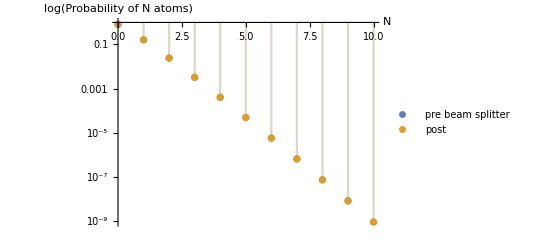

True

True

True

```mathematica
(*Check that the probability of finding a particular particle number remains the same before and after the beam splitter*)
n=0.1;(*mode occupancy*)
DiscretePlot[{PN[x,n],Pnum[x,Sqrt[n],1]},{x,0,10},ScalingFunctions->{None,"Log"},AxesLabel->{"N","log(Probability of N atoms)"},PlotLegends->{"pre beam splitter","post"}]
(*I caculated the first few terms of the expansion by hand and check those results against the definition above*)
Cf[0,0,0,0,λ,ϕ] ==(1-λ^2) (*the zeroth order*)
FullSimplify[Cf[1,0,0,1,λ,ϕ]]==FullSimplify[(1-λ^2)*λ*I*Cos[ϕ]](*a first order*)
FullSimplify[Cf[2,2,0,0,λ,ϕ]]==FullSimplify[(1-λ^2)/4*λ^2*(1+Exp[-4*I*ϕ]-2*Exp[-2*I*ϕ])](*and a second order*)
```

## Two port post selection

In this section we consider the case of only two ports (the equivalent of summing out one half of the Rarity-Tapster setup) and see if there is any useful measures to align/ anything of general interest

### Total number = 2

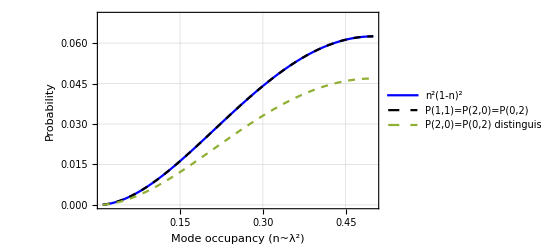

```mathematica
(*Probability of getting a given two particle state, note this probability is phase invariant*)
Plot[{1/3*PN[2,InvModOcc[x]^2] ,Pb[1, 1,InvModOcc[x], Pi/2],1/4*PN[2,InvModOcc[x]^2]}, {x, 0.01, 0.5},FrameLabel-> {"Mode occupancy (n=λ^2/(1-λ^2))", "Probability"},PlotLegends -> {"λ^4(1-λ^2)^2", "P(1,1)=P(2,0)=P(0,2)","P(2,0)=P(0,2) distinguishable"},PlotStyle -> {Blue, {Dashed, Black},Dashed},PlotRange->{{0.01,0.5},{0,0.07}}]
```

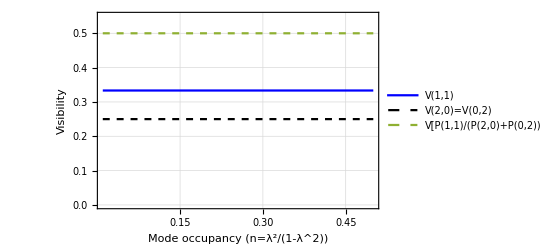

```mathematica
(*Visibiliy of the dips for the various states*)
Plot[{Vis[Pb[1,1,InvModOcc[x],Pi/2],1/2*PN[2,InvModOcc[x]^2]],Vis[Pb[2,0,InvModOcc[x],Pi/2],1/4*PN[2,InvModOcc[x]^2]],Vis[Pb[1,1,InvModOcc[x],1]/(2*Pb[0,2,InvModOcc[x],1]),1]},{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","Visibility"},PlotLegends -> {"V(1,1)", "V(2,0)=V(0,2)","V[P(1,1)/(P(2,0)+P(0,2))]"},PlotStyle -> {Blue, {Dashed, Black},Dashed},PlotRange->{{0.01,0.5},{0,0.55}}]
```

### Total number = 1

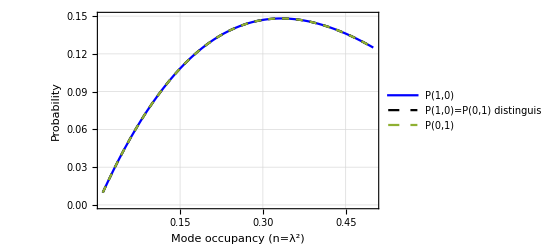

```mathematica
(*Probability of getting a given two particle state*)
Plot[{Pb[1, 0, InvModOcc[x], Pi/2.4],1/2*PN[1,InvModOcc[x]^2],Pb[0, 1, InvModOcc[x], Pi/2]}, {x, 0.01, 0.5},FrameLabel -> {"Mode occupancy (n=λ^2)","Probability"},PlotLegends -> { "P(1,0)","P(1,0)=P(0,1) distinguishable","P(0,1)"},PlotStyle -> {Blue, {Dashed, Black},Dashed},PlotRange->{{0.01,0.5},{0,0.15}}]
```

## Four port post selection

### Total pairs (particles) = 2 (4)

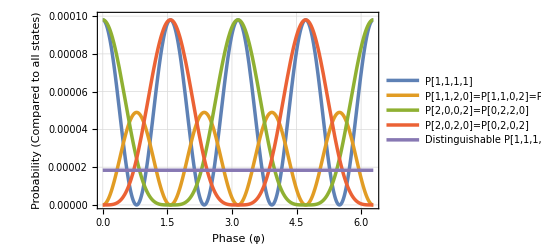

```mathematica
(*Probability against phase of all possible four port two pair states*)
Plot[{Pst[1,1,1,0.1,ϕ],Pst[1,1,2,0.1,ϕ],Pst[2,0,0,0.1,ϕ],Pst[2,0,2,0.1,ϕ],PN[2,0.01]/16},{ϕ,0,2*Pi},PlotLegends->{"P[1,1,1,1]","P[1,1,2,0]=P[1,1,0,2]=P[0,2,1,1]=P[2,0,1,1]","P[2,0,0,2]=P[0,2,2,0]","P[2,0,2,0]=P[0,2,0,2]","Distinguishable P[1,1,1,1]"},FrameLabel -> {"Phase (φ)", "Probability (Compared to all states)"},PlotRange->{{0,2*Pi},{0,0.0001}}]
```

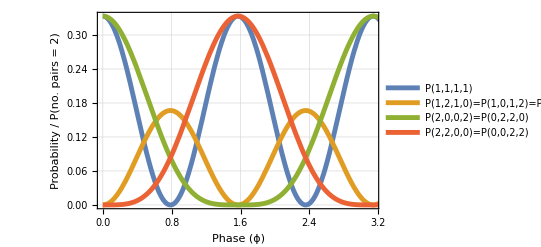

```mathematica
(*Probability against phase of all possible four port two pair states*)
Plot[{Pst[1,1,1,0.1,ϕ]/PN[2,0.1^2],Pst[1,1,2,0.1,ϕ]/PN[2,0.1^2],Pst[2,0,0,0.1,ϕ]/PN[2,0.1^2],Pst[2,0,2,0.1,ϕ]/PN[2,0.1^2]},{ϕ,0,2*Pi},PlotLegends->{"P(1,1,1,1)","P(1,2,1,0)=P(1,0,1,2)=P(0,1,2,1)=P(2,1,0,1)","P(2,0,0,2)=P(0,2,2,0)","P(2,2,0,0)=P(0,0,2,2)"},FrameLabel -> {"Phase (ϕ)", "Probability / P(no. pairs = 2)"},PlotRange->{{0,Pi},Automatic}]
```

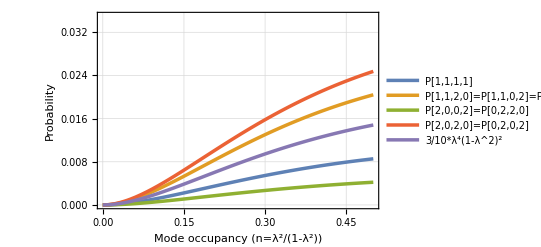

```mathematica
(*Probability of states against mode occupancy*)
Plot[{Pst[1,1,1,InvModOcc[x],1],Pst[1,1,2,InvModOcc[x],1],Pst[2,0,0,InvModOcc[x],1],Pst[2,0,2,InvModOcc[x],1],1/10*PN[2,InvModOcc[x]^2]},{x,0,0.5},PlotLegends->{"P[1,1,1,1]","P[1,1,2,0]=P[1,1,0,2]=P[0,2,1,1]=P[2,0,1,1]","P[2,0,0,2]=P[0,2,2,0]","P[2,0,2,0]=P[0,2,0,2]","3/10*λ^4(1-λ^2)^2"},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))", "Probability"},PlotRange->{{0,0.5},{0,0.035}}]
```

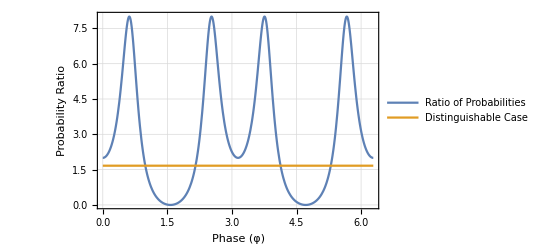

```mathematica
(*Ratio of states against phase*)
Plot[{(4*Pst[1,1,2,0.1,ϕ]+2*Pst[2,0,0,0.1,ϕ])/(Pst[1,1,1,0.1,ϕ]+2*Pst[2,0,2,0.1,ϕ]),5/3},{ϕ,0,2*Pi},PlotLegends->{"Ratio of Probabilities","Distinguishable Case"},FrameLabel -> {"Phase (φ)", "Probability Ratio"},PlotRange->{{0,2*Pi},{0,8.02}}]
```

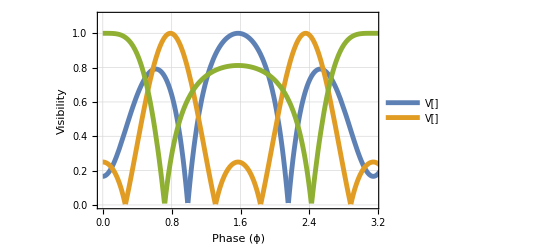

```mathematica
(*Visibility of ratio of states against phase*)
Plot[{Vis[(4*Pst[1,1,2,0.1,ϕ]+2*Pst[2,0,0,0.1,ϕ])/(Pst[1,1,1,0.1,ϕ]+2*Pst[2,0,2,0.1,ϕ]),5/3],Vis[Pst[1,1,1,0.1,ϕ]/PN[2,0.1^2],1/4],Vis[Pst[2,0,2,0.1,ϕ]/PN[2,0.1^2],1/16]},{ϕ,0,2*Pi},PlotLegends->{"V[]","V[]"},FrameLabel -> {"Phase (ϕ)", "Visibility"},PlotRange->{{0,Pi},{0,1.1}}]
```

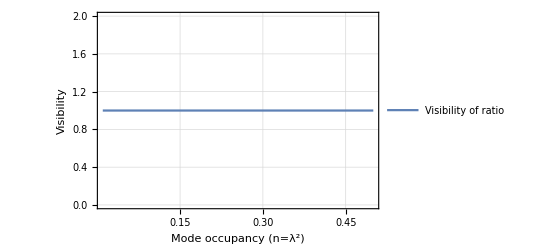

```mathematica
(*Visibility of ratio of states against mode occupancy for pi/2 phase*)
Plot[{Vis[(4*Pst[1,1,2,InvModOcc[x],Pi/2]+2*Pst[2,0,0,InvModOcc[x],Pi/2])/(Pst[1,1,1,InvModOcc[x],Pi/2]+2*Pst[2,0,2,InvModOcc[x],Pi/2]),5/3]},{x,0.01,0.5},PlotLegends->{"Visibility of ratio"},FrameLabel -> {"Mode occupancy (n=λ^2)", "Visibility"},PlotRange->{{0.01,0.5},{0,2.0}}]
```

### Total pairs (particles) = 1 (2)

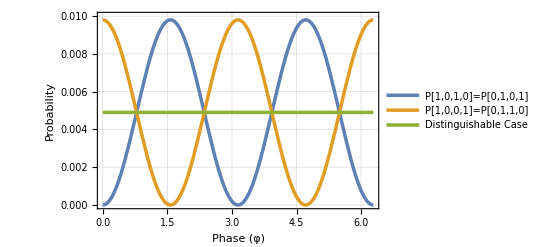

```mathematica
(*Probability against phase of all possible four port one pair states*)
Plot[{Pst[1,0,1,0.1,ϕ],Pst[1,0,0,0.1,ϕ],PN[1,0.01]/4},{ϕ,0,2*Pi},PlotLegends->{"P[1,0,1,0]=P[0,1,0,1]","P[1,0,0,1]=P[0,1,1,0]","Distinguishable Case"},FrameLabel -> {"Phase (φ)", "Probability"},PlotRange->{{0,2*Pi},{0,0.01}}]
```

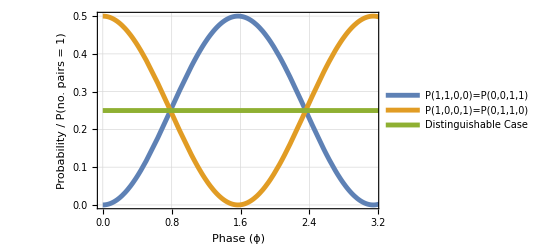

```mathematica
(*Probability against phase of all possible four port one pair states*)
Plot[{Pst[1,0,1,0.1,ϕ]/PN[1,0.1^2],Pst[1,0,0,0.1,ϕ]/PN[1,0.1^2],1/4},{ϕ,0,2*Pi},PlotLegends->{"P(1,1,0,0)=P(0,0,1,1)","P(1,0,0,1)=P(0,1,1,0)","Distinguishable Case"},FrameLabel -> {"Phase (ϕ)", "Probability / P(no. pairs = 1)"},PlotRange->{{0,Pi},Automatic}]
```

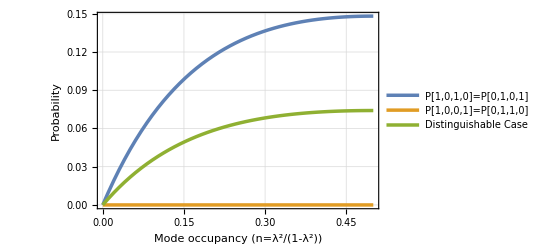

```mathematica
(*Probability against mode occupancy of all possible four port one pair states*)
Plot[{Pst[1,0,1,InvModOcc[x],Pi/2],Pst[1,0,0,InvModOcc[x],Pi/2],PN[1,InvModOcc[x]^2]/4},{x,0,0.5},PlotLegends->{"P[1,0,1,0]=P[0,1,0,1]","P[1,0,0,1]=P[0,1,1,0]","Distinguishable Case"},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))", "Probability"},PlotRange->{{0,0.5},Automatic}]
```

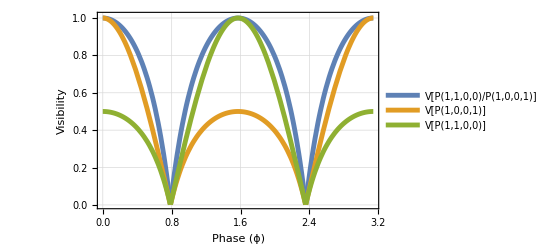

```mathematica
(*Visibility over phase of porbability ratio*)
Plot[{Vis[1,Pst[1,0,1,0.1,ϕ]/Pst[1,0,0,0.1,ϕ]],Vis[1/4,Pst[1,0,1,0.1,ϕ]/PN[1,0.1^2]],Vis[1/4,Pst[1,0,0,0.1,ϕ]/PN[1,0.1^2]]},{ϕ,0,Pi},PlotLegends->{"V[P(1,1,0,0)/P(1,0,0,1)]","V[P(1,0,0,1)]","V[P(1,1,0,0)]"},FrameLabel -> {"Phase (ϕ)", "Visibility"},PlotRange->{{0,Pi},{0,1.01}}]
```

## Coincidence and Non-coincidence

### Two port case

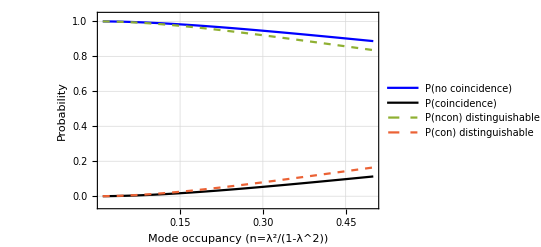

```mathematica
(*Comparison of coincidence and noncoicidence probabilities over mode occupancy for both (non)distinguisble*)
Plot[{Pnc[InvModOcc[x],Pi/2],1-Pnc[InvModOcc[x],Pi/2],Pdnc[InvModOcc[x]^2],1-Pdnc[InvModOcc[x]^2]},{x,0.01,0.5},FrameLabel->{"Mode occupancy (n=λ^2/(1-λ^2))","Probability"},PlotLegends->{"P(no coincidence)","P(coincidence)","P(ncon) distinguishable","P(con) distinguishable"},PlotStyle->{Blue,Black,Dashed,Dashed},PlotRange->{{0.01,0.5},{-0.05,1.03}}]
```

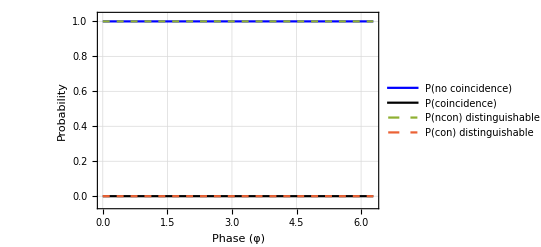

```mathematica
(*Comparison of coincidence and noncoicidence probabilities over phase for both (non)distinguisble*)
Plot[{Pnc[0.1,x],1-Pnc[0.1,x],Pdnc[0.01],1-Pdnc[0.01]},{x,0,2*Pi},FrameLabel->{"Phase (φ)", "Probability"},PlotLegends->{"P(no coincidence)","P(coincidence)","P(ncon) distinguishable","P(con) distinguishable"},PlotStyle->{Blue,Black,Dashed,Dashed},PlotRange->{{0,2*Pi},{-0.05,1.03}}]
```

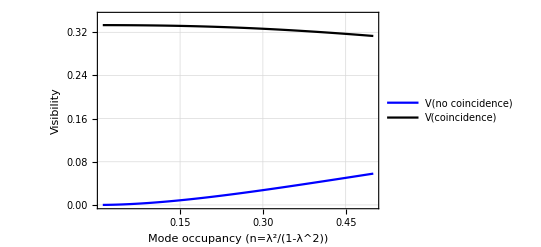

```mathematica
(*Visibility of coincidence and noncoicidence against mode occupancy*)
Plot[{Vis[ Pnc[InvModOcc[x], Pi/2],Pdnc[InvModOcc[x]^2]],Vis[ 1 - Pnc[InvModOcc[x], Pi/2],1 - Pdnc[InvModOcc[x]^2]]}, {x,0.01, 0.5},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","Visibility"},PlotLegends -> {"V(no coincidence)", "V(coincidence)"}, PlotStyle -> {Blue, Black},PlotRange->{{0.01,0.5},{0,0.35}}]
```

### Four port case

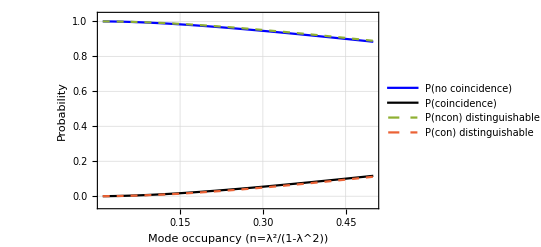

```mathematica
(*Comparison of coincidence and noncoicidence probabilities over mode occupancy for both (non)distinguisble*)
Plot[{Pnc4[InvModOcc[x],Pi/2],1-Pnc4[InvModOcc[x],Pi/2],Pdnc4[InvModOcc[x]^2],1-Pdnc4[InvModOcc[x]^2]},{x,0.01,0.5},FrameLabel->{"Mode occupancy (n=λ^2/(1-λ^2))","Probability"},PlotLegends->{"P(no coincidence)","P(coincidence)","P(ncon) distinguishable","P(con) distinguishable"},PlotStyle->{Blue,Black,Dashed,Dashed},PlotRange->{{0.01,0.5},{-0.05,1.03}}]
```

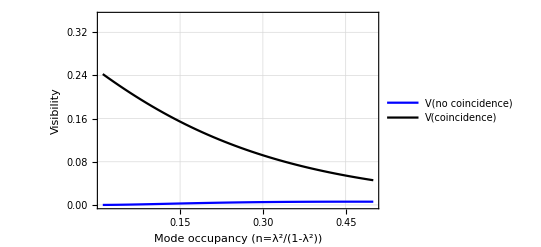

```mathematica
(*Visibility of coincidence and noncoicidence against mode occupancy*)
Plot[{Vis[ Pnc4[InvModOcc[x], Pi/2],Pdnc4[InvModOcc[x]^2]],Vis[ 1 - Pnc4[InvModOcc[x], Pi/2],1 - Pdnc4[InvModOcc[x]^2]]}, {x,0.01, 0.5},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","Visibility"},PlotLegends -> {"V(no coincidence)", "V(coincidence)"}, PlotStyle -> {Blue, Black},PlotRange->{{0.01,0.5},{0,0.35}}]
```

## g^(2)

Next we consider the various possible two particle correlation functions (g^(2) for short) that can be constructed between the four ports of our Rarity-Tapster interferometer (3!=6 in total)

```mathematica
Ord=5;(*To what order in particle number we wish to calculate the g2's*)
```

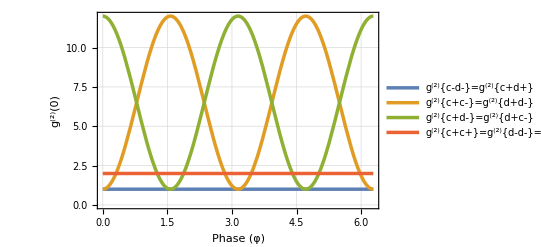

```mathematica
(*main g2's against phase for mode occupancy=0.01, note these equalities hold in the distinguishable case also*)
Plot[{g2cmdm[InvModOcc[0.1],ϕ,Ord],g2cpcm[InvModOcc[0.1],ϕ,Ord],g2cpdm[InvModOcc[0.1],ϕ,Ord],g2cpcp[InvModOcc[0.1],ϕ,Ord]},{ϕ,0,2*Pi},PlotLegends->{"g^(2){c-d-}=g^(2){c+d+}","g^(2){c+c-}=g^(2){d+d-}","g^(2){c+d-}=g^(2){d+c-}","g^(2){c+c+}=g^(2){d-d-}=g^(2){c+c+}=g^(2){d+d+}"},FrameLabel -> {"Phase (φ)", "g^(2)(0)"},PlotRange->{{0,2*Pi},Automatic}]
```

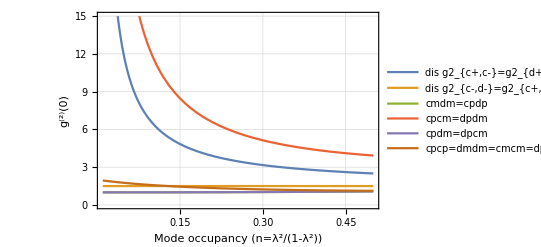

```mathematica
(*The six possible g2's along with their distinguishable counter parts*)
ϕ1=Pi/2;
Plot[{1/(2*InvModOcc[x]^2)+1,3/2,g2cmdm[InvModOcc[x],ϕ1,Ord],g2cpcm[InvModOcc[x],ϕ1,Ord],g2cpdm[InvModOcc[x],ϕ1,Ord],g2cpcp[InvModOcc[x],ϕ1,Ord]},{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","g^(2)(0)"},PlotLegends -> {"dis g2_{c+,c-}=g2_{d+,d-}=g2_{d+,c-}=g2_{c+,d-}","dis g2_{c-,d-}=g2_{c+,d+}=g2_cl{c+}","cmdm=cpdp","cpcm=dpdm","cpdm=dpcm","cpcp=dmdm=cmcm=dpdp"},PlotRange->{{0.01,0.5},{0,15}}]
```

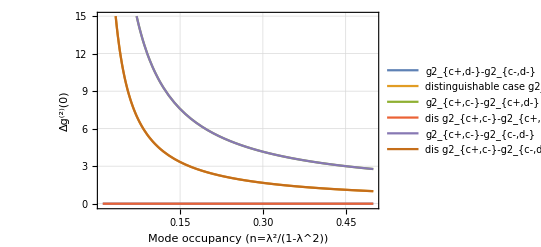

```mathematica
(*An interesting comparison differences of the g2's*)
Plot[{g2cpdm[InvModOcc[x],Pi/2,Ord]-g2cmdm[InvModOcc[x],Pi/2,Ord],1/(2*InvModOcc[x]^2)+1-3/2,g2cpcm[InvModOcc[x],Pi/2,Ord]-g2cpdm[InvModOcc[x],Pi/2,Ord],0,g2cpcm[InvModOcc[x],Pi/2,Ord]-g2cmdm[InvModOcc[x],Pi/2,Ord],1/(2*InvModOcc[x]^2)+1-3/2},{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","Δg^(2)(0)"},PlotLegends -> {"g2_{c+,d-}-g2_{c-,d-}","distinguishable case g2_{c+,d-}-g2_{c-,d-}","g2_{c+,c-}-g2_{c+,d-}","dis g2_{c+,c-}-g2_{c+,d-}","g2_{c+,c-}-g2_{c-,d-}","dis g2_{c+,c-}-g2_{c-,d-}"},PlotRange->{{0.01,0.5},{-0.1,15}}]
```

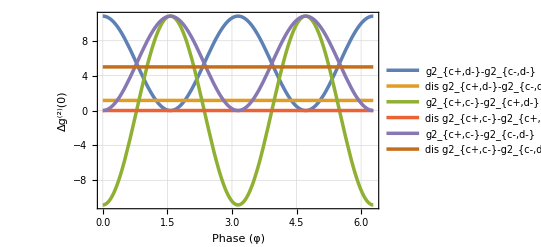

```mathematica
(*Same comparison but for phase*)
nplot=InvModOcc[0.1];
Plot[{g2cpdm[nplot,ϕ,Ord]-g2cmdm[nplot,ϕ,Ord],1/(2*nplot)+1-3/2,g2cpcm[nplot,ϕ,Ord]-g2cpdm[nplot,ϕ,Ord],0,g2cpcm[nplot,ϕ,Ord]-g2cmdm[nplot,ϕ,Ord],1/(2*nplot^2)+1-3/2},{ϕ,0,2*Pi},FrameLabel -> {"Phase (φ)","Δg^(2)(0)"},PlotLegends ->  {"g2_{c+,d-}-g2_{c-,d-}","dis g2_{c+,d-}-g2_{c-,d-}","g2_{c+,c-}-g2_{c+,d-}","dis g2_{c+,c-}-g2_{c+,d-}","g2_{c+,c-}-g2_{c-,d-}","dis g2_{c+,c-}-g2_{c-,d-}"},PlotRange->{{0,2*Pi},Automatic}]
```

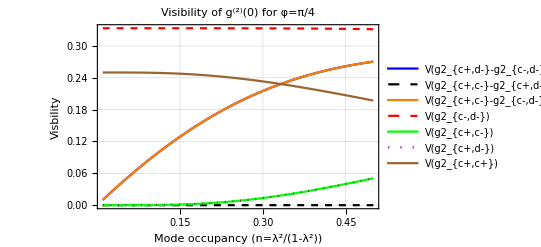

```mathematica
(*Visibility for g2's and dif g2's for φ=π/4*)
ϕplot=Pi/4;
Plot[{Vis[g2cpdm[InvModOcc[x],ϕplot,Ord]-g2cmdm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1-3/2],
0(*Vis[g2cpcm[InvModOcc[x],ϕplot,Ord]-g2cpdm[InvModOcc[x],ϕplot,Ord],0]*),
Vis[g2cpcm[InvModOcc[x],ϕplot,Ord]-g2cmdm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1-3/2],
Vis[g2cmdm[InvModOcc[x],ϕplot,Ord],3/2],
Vis[g2cpcm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1],
Vis[g2cpdm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1],
Vis[g2cpcp[InvModOcc[x],ϕplot,Ord],3/2]},{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","Visbility"},PlotLegends -> {"V(g2_{c+,d-}-g2_{c-,d-})","V(g2_{c+,c-}-g2_{c+,d-})","V(g2_{c+,c-}-g2_{c-,d-})","V(g2_{c-,d-})","V(g2_{c+,c-})","V(g2_{c+,d-})","V(g2_{c+,c+})"},PlotStyle->{Blue,{Black,Dashed},Orange,{Red,Dashed},Green,{Purple,Dotted},Brown},PlotRange->{{0.01,0.5},Automatic},PlotLabel->"Visibility of g^(2)(0) for φ=π/4"]
```

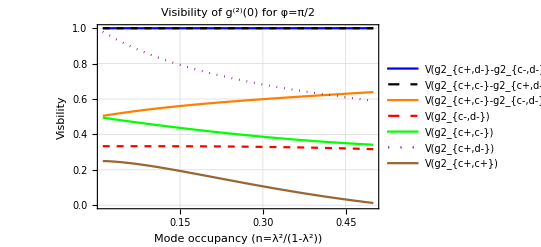

```mathematica
(*Visibility for g2's and dif g2's for φ=π/2*)
ϕplot=Pi/2;
Plot[{Vis[g2cpdm[InvModOcc[x],ϕplot,Ord]-g2cmdm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1-3/2],
Vis[g2cpcm[InvModOcc[x],ϕplot,Ord]-g2cpdm[InvModOcc[x],ϕplot,Ord],0],
Vis[g2cpcm[InvModOcc[x],ϕplot,Ord]-g2cmdm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1-3/2],
Vis[g2cmdm[InvModOcc[x],ϕplot,Ord],3/2],
Vis[g2cpcm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1],
Vis[g2cpdm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1],
Vis[g2cpcp[InvModOcc[x],ϕplot,Ord],3/2]},{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","Visbility"},PlotLegends -> {"V(g2_{c+,d-}-g2_{c-,d-})","V(g2_{c+,c-}-g2_{c+,d-})","V(g2_{c+,c-}-g2_{c-,d-})","V(g2_{c-,d-})","V(g2_{c+,c-})","V(g2_{c+,d-})","V(g2_{c+,c+})"},PlotStyle->{Blue,{Black,Dashed},Orange,{Red,Dashed},Green,{Purple,Dotted},Brown},PlotRange->{{0.01,0.5},Automatic},PlotLabel->"Visibility of g^(2)(0) for φ=π/2"]
```

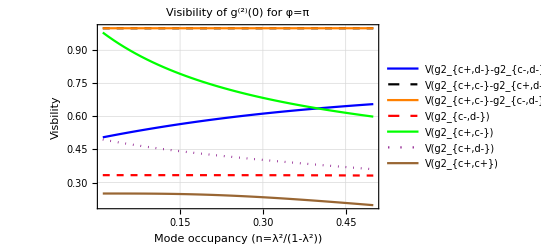

```mathematica
(*Visibility for g2's and dif g2's for φ=π*)
ϕplot=Pi;
Plot[{Vis[g2cpdm[InvModOcc[x],ϕplot,Ord]-g2cmdm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1-3/2],
Vis[g2cpcm[InvModOcc[x],ϕplot,Ord]-g2cpdm[InvModOcc[x],ϕplot,Ord],0],
Vis[g2cpcm[InvModOcc[x],ϕplot,Ord]-g2cmdm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1-3/2],
Vis[g2cmdm[InvModOcc[x],ϕplot,Ord],3/2],
Vis[g2cpcm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1],
Vis[g2cpdm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1],
Vis[g2cpcp[InvModOcc[x],ϕplot,Ord],3/2]},{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","Visbility"},PlotLegends -> {"V(g2_{c+,d-}-g2_{c-,d-})","V(g2_{c+,c-}-g2_{c+,d-})","V(g2_{c+,c-}-g2_{c-,d-})","V(g2_{c-,d-})","V(g2_{c+,c-})","V(g2_{c+,d-})","V(g2_{c+,c+})"},PlotStyle->{Blue,{Black,Dashed},Orange,{Red,Dashed},Green,{Purple,Dotted},Brown},PlotRange->{{0.01,0.5},Automatic},PlotLabel->"Visibility of g^(2)(0) for φ=π"]
```

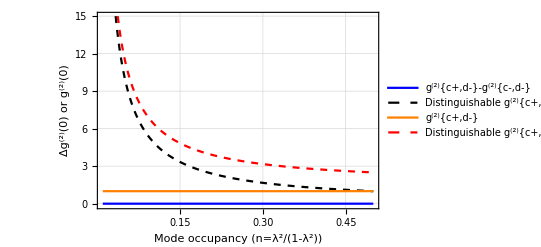

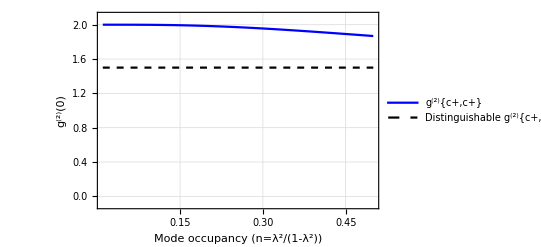

```mathematica
(*For group Talk*)
Plot[{g2cpdm[InvModOcc[x],Pi/2,Ord]-g2cmdm[InvModOcc[x],Pi/2,Ord],1/(2*InvModOcc[x]^2)+1-3/2,g2cpdm[InvModOcc[x],Pi/2,Ord],1/(2*InvModOcc[x]^2)+1},{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","Δg^(2)(0) or g^(2)(0)"},PlotLegends -> {"g^(2){c+,d-}-g^(2){c-,d-}","Distinguishable g^(2){c+,d-}-g^(2){c-,d-}","g^(2){c+,d-}","Distinguishable g^(2){c+,d-}"},PlotRange->{{0.01,0.5},{-0.1,15}},PlotStyle->{Blue,{Black,Dashed},Orange,{Red,Dashed},Green,{Purple,Dotted},Brown}]
Plot[{g2cpcp[InvModOcc[x],Pi/2,Ord],3/2},{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","g^(2)(0)"},PlotLegends -> {"g^(2){c+,c+}","Distinguishable g^(2){c+,c+}"},PlotRange->{{0.01,0.5},{-0.1,2.1}},PlotStyle->{Blue,{Black,Dashed},Orange,{Red,Dashed},Green,{Purple,Dotted},Brown}]
```

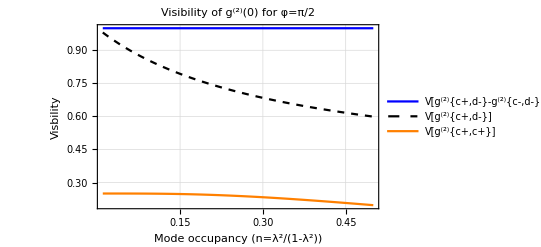

```mathematica
ϕplot=Pi/2;
Plot[{Vis[g2cpdm[InvModOcc[x],ϕplot,Ord]-g2cmdm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1-3/2],
Vis[g2cpdm[InvModOcc[x],ϕplot,Ord],1/(2*InvModOcc[x]^2)+1],
Vis[g2cpcp[InvModOcc[x],ϕplot,Ord],3/2]
},{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","Visbility"},PlotLegends -> {"V[g^(2){c+,d-}-g^(2){c-,d-}]","V[g^(2){c+,d-}]","V[g^(2){c+,c+}]"},PlotStyle->{Blue,{Black,Dashed},Orange,{Red,Dashed},Green,{Purple,Dotted},Brown},PlotRange->{{0.01,0.5},Automatic},PlotLabel->"Visibility of g^(2)(0) for φ=π/2"]
```

## g^(n) and beyond

```mathematica
Ordg4=3;(*To what order in particle number we wish to calculate the g2's*)
```

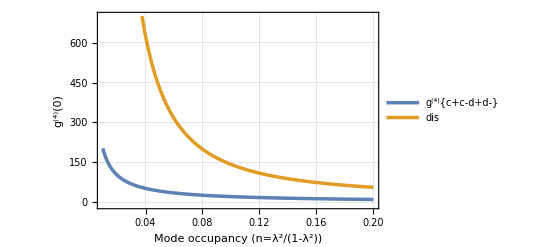

```mathematica
(*g^(4) correlator for the system*)
Plot[{g4cpdpcmdm[InvModOcc[x],Pi/4,Ordg4],3/4*(1/InvModOcc[x]^4+6/InvModOcc[x]^2+3)},{x,0.01,0.2},PlotLegends -> {"g^(4){c+c-d+d-}","dis"},PlotRange->{{0.01,0.2},{-10,700}},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","g^(4)(0)"}]
```

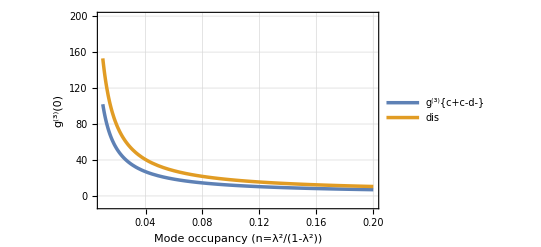

```mathematica
Plot[{g3cpcmdm[InvModOcc[x],Pi/2,Ordg4],3/2*(1/InvModOcc[x]^2+1)},{x,0.01,0.2},PlotLegends -> {"g^(3){c+c-d-}","dis"},PlotRange->{{0.01,0.2},{-10,200}},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","g^(3)(0)"}]
```

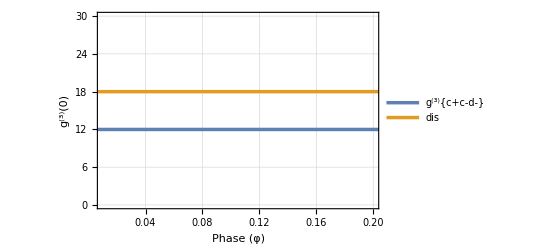

```mathematica
Plot[{g3cpcmdm[InvModOcc[0.1],ϕ,Ordg4],3/2*(1/InvModOcc[0.1]^2+1)},{ϕ,0,2*Pi},PlotLegends -> {"g^(3){c+c-d-}","dis"},PlotRange->{{0.01,0.2},{0,30}},FrameLabel -> {"Phase (φ)","g^(3)(0)"}]
```

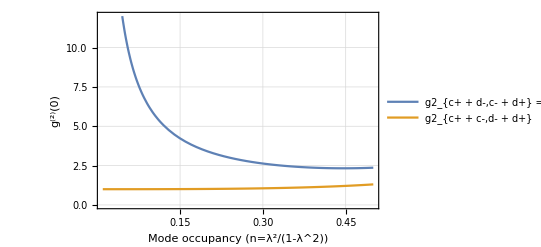

```mathematica
(*The six possible g2's*)
Plot[{(Ecpcm[Sqrt[x],Pi/2,Ord]+Ecmdm[Sqrt[x],Pi/2,Ord]+Ecpdp[Sqrt[x],Pi/2,Ord]+Edpdm[Sqrt[x],Pi/2,Ord])/((Ecm[Sqrt[x],Pi/2,Ord]+Edp[Sqrt[x],Pi/2,Ord])*(Ecp[Sqrt[x],Pi/2,Ord]+Edm[Sqrt[x],Pi/2,Ord])),(Ecpdm[Sqrt[x],Pi/2,Ord]+Ecmdm[Sqrt[x],Pi/2,Ord]+Ecpdp[Sqrt[x],Pi/2,Ord]+Edpcm[Sqrt[x],Pi/2,Ord])/((Ecm[Sqrt[x],Pi/2,Ord]+Ecp[Sqrt[x],Pi/2,Ord])*(Edp[Sqrt[x],Pi/2,Ord]+Edm[Sqrt[x],Pi/2,Ord]))},{x,0.01,0.5},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))","g^(2)(0)"},PlotLegends -> {"g2_{c+ + d-,c- + d+} = g2_{c+ + d+,c- + d-}","g2_{c+ + c-,d- + d+}"},PlotRange->{{0.01,0.5},{0,12}}]
```

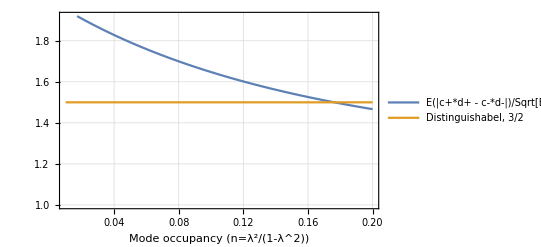

```mathematica
(*Normalised expected difference of the product across halves*)
Plot[{Edif[InvModOcc[x],Pi/4,Ord]/Sqrt[(Ecp[InvModOcc[x],Pi/4,Ord]*Ecm[InvModOcc[x],Pi/4,Ord]*Edm[InvModOcc[x],Pi/4,Ord]*Edp[InvModOcc[x],Pi/4,Ord])],3/2},{x,0.01,0.2},PlotLegends -> {"E(|c+*d+ - c-*d-|)/Sqrt[E*E*E*E]","Distinguishabel, 3/2"},PlotRange->{{0.01,0.2},{1,1.92}},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))"}]
```

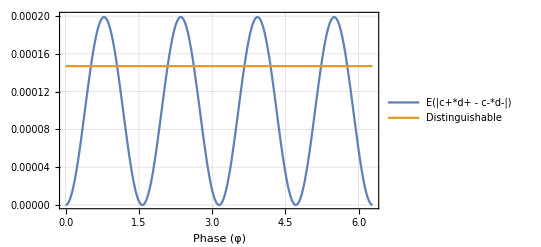

```mathematica
Plot[{Edif[0.1,ϕ,Ord],3/2*0.1^4*(1-0.1^2)^2},{ϕ,0,2*Pi},PlotLegends -> {"E(|c+*d+ - c-*d-|)","Distinguishable"},PlotRange->{{0,2*Pi},{0,0.0002}},FrameLabel -> {"Phase (φ)"}]
```

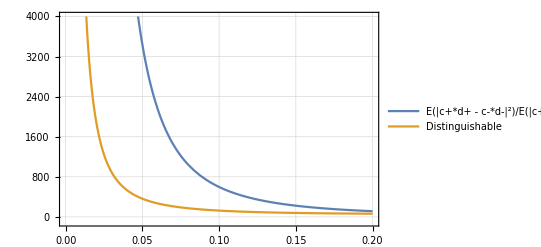

```mathematica
(*Expected value of the magnitude of the difference across both halves, note this should be independant of single pair states*)
Plot[{(Ecpcm2[Sqrt[x],Pi/4,Ord]+Edpdm2[Sqrt[x],Pi/4,Ord]-2*Ecpdpcmdm[Sqrt[x],Pi/4,Ord])/((Edif[Sqrt[x],Pi/4,Ord])^2),2/3*1/((1-x)^6*x^2)},{x,0.01,0.2},PlotLegends -> {"E(|c+*d+ - c-*d-|^2)/E(|c+*d+ - c-*d-|)^2}","Distinguishable"},PlotRange->{{0,0.2},{-100,4000}}]
```

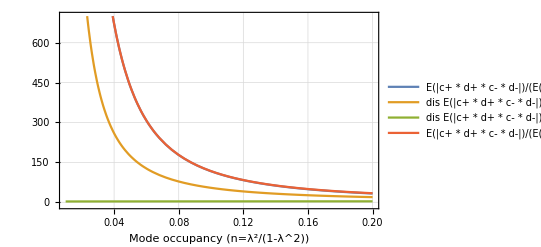

```mathematica
(*Expected value of the product of all four ports*)
Plot[{Ecpdpcmdm[Sqrt[x],Pi/2,Ord]/(Ecpdp[Sqrt[x],Pi/2,Ord]*Ecmdm[Sqrt[x],Pi/2,Ord]),1+1/(3*x^2)+2/x,(3+9*x*(2+x))/(1+2*x)^2,Ecpdpcmdm[Sqrt[x],Pi/2,Ord]/(Ecp[Sqrt[x],Pi/2,Ord]*Ecm[Sqrt[x],Pi/2,Ord]*Edm[Sqrt[x],Pi/2,Ord]*Edp[Sqrt[x],Pi/2,Ord])},{x,0.01,0.2},PlotLegends -> {"E(|c+ * d+ * c- * d-|)/(E(|c+ * d+|)*E(|c- * d-|))=E(|c+ * d+ * c- * d-|)/(E(|c+ * d-|)*E(|c- * d+|)","dis E(|c+ * d+ * c- * d-|)/(E(|c+ * d+|)*E(|c- * d-|))","dis E(|c+ * d+ * c- * d-|)/(E(|c+ * d-|)*E(|c- * d+|)","E(|c+ * d+ * c- * d-|)/(E(|c+|)*E(|c-|)*E(|d+|)*E(|d-|))"},PlotRange->{{0.01,0.2},{-10,700}},FrameLabel -> {"Mode occupancy (n=λ^2/(1-λ^2))"}]
```

```mathematica
(*becnh mark comparison*)
```

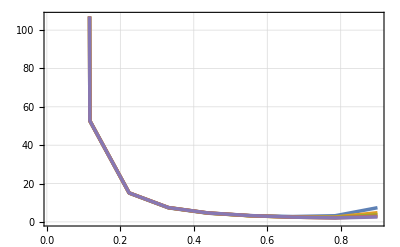
{9.45313,-Graphics-}

```mathematica
Timing[Plot[{g2dpdm[x,1,2],g2dpdm[x,1,3],g2dpdm[x,1,4],g2dpdm[x,1,5],g2dpdm[x,1,6]},{x,0.01,0.9},PlotPoints->3,MaxRecursion->2]]
```

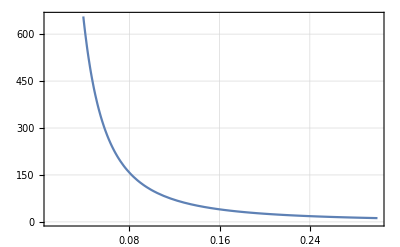
{6.89063,-Graphics-}

```mathematica
f[x_]:=FullSimplify[g2cpcmC[x,Pi/2]]
Timing[Plot[f[x],{x,0.01,0.3}]]
```

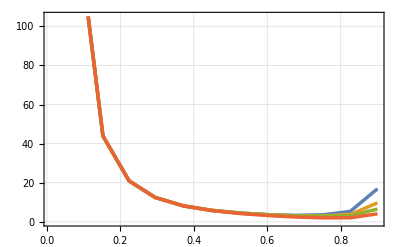
{11.5,-Graphics-}

```mathematica
Timing[Plot[{g3cpcmdm[x,1,3],g3cpcmdm[x,1,4],g3cpcmdm[x,1,5],g3cpdpdm[x,1,5]},{x,0.01,0.9},PlotPoints->4,MaxRecursion->2]]
```

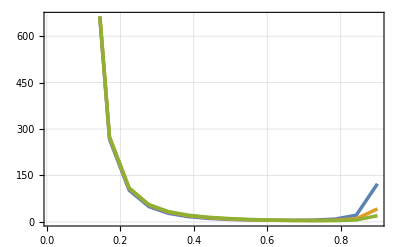
{4.1875,-Graphics-}

```mathematica
Timing[Plot[{g4cpdpcmdm[x,1,2],g4cpdpcmdm[x,1,3],g4cpdpcmdm[x,1,4]},{x,0.01,0.9},PlotPoints->3,MaxRecursion->3]]
```

```mathematica
Plot3D[Pstate[1,5,1,InvModOcc[0.1],ϕ,θ],{ϕ,0,2*Pi},{θ,0,2*Pi}]
```

-Graphics3D-

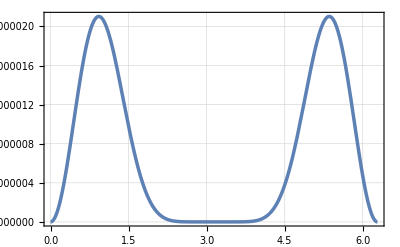

```mathematica
Plot[Pstate[0,5,1,InvModOcc[0.1],ϕ,Pi],{ϕ,0,2*Pi}]
```

## Quantum Entropy

### Th

```mathematica
Cf[0,0,0,0,λ,2*ϕ]
```

1-λ^2

```mathematica
FullSimplify[Refine[Cf[1,1,0,0,λ,2*ϕ]*Conjugate[Cf[1,1,0,0,λ,2*ϕ]],{Element[ϕ,Reals],Element[λ,Reals]}]]
Assuming[ϕ∈Reals&&λ>0,FullSimplify[Pst[1,0,1,λ,2*ϕ]]]
```

λ^2 (-1+λ^2)^2 Sin[2 ϕ]^2

1/4 Abs[(1-ⅇ^(-4 ⅈ ϕ)) λ (1-λ^2)]^2

1/4 Abs[λ (1-λ^2) (1-Cos[4 ϕ]+ⅈ Sin[4 ϕ])]^2

1/4 Abs[(-1+ⅇ^(-4 ⅈ ϕ)) λ (-1+λ^2)]^2

```mathematica
Cf[1,0,0,1,λ,2*ϕ]
FullSimplify[Refine[Cf[1,0,0,1,λ,2*ϕ]*Conjugate[Cf[1,0,0,1,λ,2*ϕ]],{Element[ϕ,Reals],Element[λ,Reals]}]]
```

1/2 (ⅈ ⅇ^(-2 ⅈ ϕ)+ⅈ ⅇ^(2 ⅈ ϕ)) λ (1-λ^2)

λ^2 (-1+λ^2)^2 Cos[2 ϕ]^2

```mathematica
Cf[0,0,1,1,λ,2*ϕ]
FullSimplify[Refine[Cf[0,0,1,1,λ,2*ϕ]*Conjugate[Cf[0,0,1,1,λ,2*ϕ]],{Element[ϕ,Reals],Element[λ,Reals]}]]
```

1/2 (1-ⅇ^(4 ⅈ ϕ)) λ (1-λ^2)

λ^2 (-1+λ^2)^2 Sin[2 ϕ]^2

```mathematica
Cf[0,1,1,0,λ,2*ϕ]
FullSimplify[Refine[Cf[0,1,1,0,λ,2*ϕ]*Conjugate[Cf[0,1,1,0,λ,2*ϕ]],{Element[ϕ,Reals],Element[λ,Reals]}]]
```

1/2 (ⅈ ⅇ^(-2 ⅈ ϕ)+ⅈ ⅇ^(2 ⅈ ϕ)) λ (1-λ^2)

λ^2 (-1+λ^2)^2 Cos[2 ϕ]^2

-(4 λ^2 Log[1/λ])/(-1+λ^2)

```mathematica
(*Two pair states*)
```

```mathematica
Cf[1,1,1,1,λ,2*ϕ]
FullSimplify[Refine[Cf[1,1,1,1,λ,2*ϕ]*Conjugate[Cf[1,1,1,1,λ,2*ϕ]],{Element[ϕ,Reals],Element[λ,Reals]}]]
```

1/4 (-2 ⅇ^(-4 ⅈ ϕ)-2 ⅇ^(4 ⅈ ϕ)) λ^2 (1-λ^2)

λ^4 (-1+λ^2)^2 Cos[4 ϕ]^2

```mathematica
Cf[2,0,0,2,λ,2*ϕ]
FullSimplify[Refine[Cf[2,0,0,2,λ,2*ϕ]*Conjugate[Cf[2,0,0,2,λ,2*ϕ]],{Element[ϕ,Reals],Element[λ,Reals]}]]
```

1/2 (-1-1/2 ⅇ^(-4 ⅈ ϕ)-1/2 ⅇ^(4 ⅈ ϕ)) λ^2 (1-λ^2)

λ^4 (-1+λ^2)^2 Cos[2 ϕ]^4

```mathematica
Cf[2,2,0,0,λ,2*ϕ]
FullSimplify[Refine[Cf[2,2,0,0,λ,2*ϕ]*Conjugate[Cf[2,2,0,0,λ,2*ϕ]],{Element[ϕ,Reals],Element[λ,Reals]}]]
```

1/2 (1/2-ⅇ^(-4 ⅈ ϕ)+1/2 ⅇ^(-8 ⅈ ϕ)) λ^2 (1-λ^2)

λ^4 (-1+λ^2)^2 Sin[2 ϕ]^4

```mathematica
Cf[1,2,1,0,λ,2*ϕ]
FullSimplify[Refine[Cf[1,2,1,0,λ,2*ϕ]*Conjugate[Cf[1,2,1,0,λ,2*ϕ]],{Element[ϕ,Reals],Element[λ,Reals]}]]
```

((ⅈ ⅇ^(2 ⅈ ϕ)-ⅈ ⅇ^(-6 ⅈ ϕ)) λ^2 (1-λ^2))/(2 √2)

1/2 λ^4 (-1+λ^2)^2 Sin[4 ϕ]^2

```mathematica
(*von Nuemon entropy*)
FullSimplify[(1-λ^2)^2*Sum[λ^(2*Nn)*2*Nn*(Nn+1),{Nn,0,Infinity}]*Log[1/λ]]
(*Renyi entropy*)
FullSimplify[-Log[(1-λ^2)^4*Sum[λ^(4*Nn)*(Nn+1),{Nn,0,Infinity}]]]
(*Renyi entropy subsystem*)
FullSimplify[-Log[(1-λ^2)^2*Sum[λ^(2*i),{i,0,Infinity}]]]
(*Parity*)
FullSimplify[(1-λ^2)^2*Sum[Sum[λ^(2*(i+j))*(-1)^i,{i,0,Infinity}],{j,0,Infinity}]]
FullSimplify[(1-λ^2)^2*Sum[λ^(2*Nn),{Nn,0,Infinity}]]
FullSimplify[(1-λ^2)^2*Sum[Sum[λ^(2*(i+j)),{i,0,Infinity}],{j,0,Infinity}]]
```

-(4 λ^2 Log[1/λ])/(-1+λ^2)

-Log[((-1+λ^2)^2)/((1+λ^2)^2)]

-Log[1-λ^2]

-1+2/(1+λ^2)

1-λ^2

1

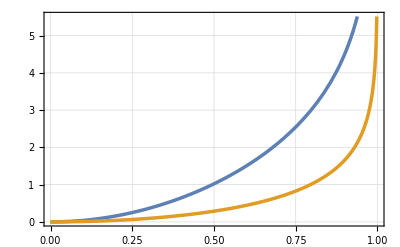

```mathematica
Plot[{-Log[((-1+λ^2)^2)/((1+λ^2)^2)],-Log[1-λ^2]},{λ,0,1}]
```

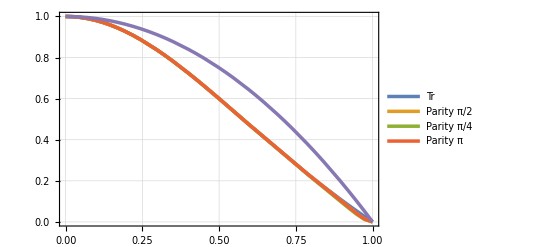

```mathematica
Parity[λ_,p_,ϕ_]:=Sum[Sum[Sum[(-1)^p*Pst[Y,W,X,λ,ϕ],{W,0,6}],{X,0,6}],{Y,0,6}]
Plot[{(1-λ^2)/(1+λ^2),Parity[λ,Y,Pi/2],Parity[λ,Y,Pi/4],Parity[λ,Y,Pi],1-λ^2},{λ,0,1},PlotPoints->6,MaxRecursion->3,PlotLegends -> {"Tr","Parity π/2","Parity π/4","Parity π"}]
```

```mathematica
FullSimplify[(1-λ^2)/(1+λ^2)]
```

-1+2/(1+λ^2)

```mathematica
Sum[Cf[l,i+j-l,A,i+j-A,λ,Pi/2]*Conjugate[Cf[i,j,A,i+j-A,λ,Pi/2]]*Cf[i,j,k,i+j-k,λ,Pi/2]*Conjugate[Cf[l,i+j-l,k,i+j-k,λ,Pi/2]],{i,0,12},{j,0,12},{A,0,i+j},{k,0,i+j},{l,0,i+j}];
```

```mathematica
%143
```

(1-λ^2)^2 (1-Conjugate[λ]^2)^2+64 λ^2 (1-λ^2)^2 Conjugate[λ]^2 (1-Conjugate[λ]^2)^2+16 λ^3 (1-λ^2)^2 Conjugate[λ]^3 (1-Conjugate[λ]^2)^2+25/16 λ^4 (1-λ^2)^2 Conjugate[λ]^4 (1-Conjugate[λ]^2)^2+1/16 λ^5 (1-λ^2)^2 Conjugate[λ]^5 (1-Conjugate[λ]^2)^2+(9346249 λ^6 (1-λ^2)^2 Conjugate[λ]^6 (1-Conjugate[λ]^2)^2)/9216+2663/96 λ^7 (1-λ^2)^2 Conjugate[λ]^7 (1-Conjugate[λ]^2)^2+(166463 λ^8 (1-λ^2)^2 Conjugate[λ]^8 (1-Conjugate[λ]^2)^2)/165888+(137 λ^9 (1-λ^2)^2 Conjugate[λ]^9 (1-Conjugate[λ]^2)^2)/3072+(2075 λ^10 (1-λ^2)^2 Conjugate[λ]^10 (1-Conjugate[λ]^2)^2)/12582912

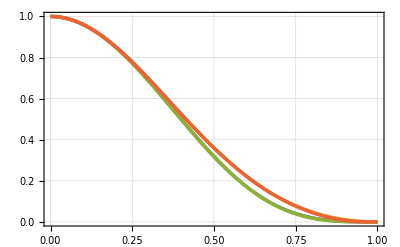

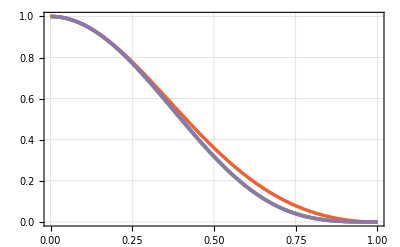

General::munfl: 1.47424×10^-169 1.47424×10^-169 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.56756×10^-188 2.56756×10^-188 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.47424×10^-169 1.47424×10^-169 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

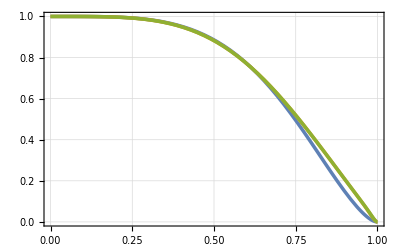

```mathematica
Plot[{(1-λ^2)^2 (1-Conjugate[λ]^2)^2+λ^4 (1-λ^2)^2 Conjugate[λ]^4 (1-Conjugate[λ]^2)^2+λ^8 (1-λ^2)^2 Conjugate[λ]^8 (1-Conjugate[λ]^2)^2+λ^12 (1-λ^2)^2 Conjugate[λ]^12 (1-Conjugate[λ]^2)^2+λ^16 (1-λ^2)^2 Conjugate[λ]^16 (1-Conjugate[λ]^2)^2+λ^20 (1-λ^2)^2 Conjugate[λ]^20 (1-Conjugate[λ]^2)^2+λ^24 (1-λ^2)^2 Conjugate[λ]^24 (1-Conjugate[λ]^2)^2+λ^28 (1-λ^2)^2 Conjugate[λ]^28 (1-Conjugate[λ]^2)^2+λ^32 (1-λ^2)^2 Conjugate[λ]^32 (1-Conjugate[λ]^2)^2,((1-λ^2)/(1+λ^2))^2,%243,%248},{λ,0,1}]
Plot[{%202,%208,%211,%217,%220},{λ,0,1}]
Plot[{%220/((1-λ^2)/(1+λ^2))^2,%266/((1-λ^2)/(1+λ^2))^2,%271/((1-λ^2)/(1+λ^2))^2},{λ,0,1}]
```

```mathematica
NumberForm[16.49314088636159,16]
```

16.49314088636159

```mathematica
%40
```

16 (1-λ^2)^2 (1-Conjugate[λ]^2)^2+225/2 λ (1-λ^2)^2 Conjugate[λ] (1-Conjugate[λ]^2)^2+3499/8 λ^2 (1-λ^2)^2 Conjugate[λ]^2 (1-Conjugate[λ]^2)^2+181567/192 λ^3 (1-λ^2)^2 Conjugate[λ]^3 (1-Conjugate[λ]^2)^2+(44911585 λ^4 (1-λ^2)^2 Conjugate[λ]^4 (1-Conjugate[λ]^2)^2)/36864+(1088669 λ^5 (1-λ^2)^2 Conjugate[λ]^5 (1-Conjugate[λ]^2)^2)/2304+(43000453 λ^6 (1-λ^2)^2 Conjugate[λ]^6 (1-Conjugate[λ]^2)^2)/331776+(11238883 λ^7 (1-λ^2)^2 Conjugate[λ]^7 (1-Conjugate[λ]^2)^2)/589824+(7903233 λ^8 (1-λ^2)^2 Conjugate[λ]^8 (1-Conjugate[λ]^2)^2)/4194304

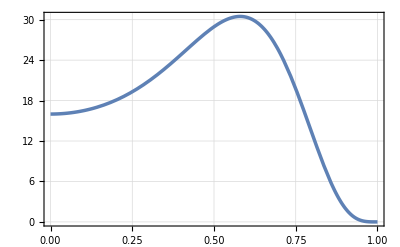

```mathematica
Plot[%41,{λ,0,1}]
```

```mathematica
%38
```

16 (1-λ^2)^2 (1-Conjugate[λ]^2)^2+2 λ (1-λ^2)^2 Conjugate[λ] (1-Conjugate[λ]^2)^2+1/2 (ⅈ ⅇ^(-ⅈ ϕ)+ⅈ ⅇ^(ⅈ ϕ)) (-ⅈ ⅇ^(-ⅈ Conjugate[ϕ])-ⅈ ⅇ^(ⅈ Conjugate[ϕ])) λ (1-λ^2)^2 Conjugate[λ] (1-Conjugate[λ]^2)^2+(ⅈ ⅇ^(-ⅈ ϕ)+2 ⅈ ⅇ^(ⅈ ϕ)) (-ⅈ ⅇ^(-ⅈ Conjugate[ϕ])-ⅈ ⅇ^(ⅈ Conjugate[ϕ])) λ (1-λ^2)^2 Conjugate[λ] (1-Conjugate[λ]^2)^2+1057+1/256 (1/4-1/2 ⅇ^(2 ⅈ ϕ)+1/4 ⅇ^(4 ⅈ ϕ)) (1+3/2 ⅇ^(-4 ⅈ ϕ)+3/2 ⅇ^(4 ⅈ ϕ)) (1/4-1/2 ⅇ^(-2 ⅈ Conjugate[ϕ])+1/4 ⅇ^(-4 ⅈ Conjugate[ϕ])) (1+3/2 ⅇ^(-4 ⅈ Conjugate[ϕ])+3/2 ⅇ^(4 ⅈ Conjugate[ϕ])) λ^8 (1-λ^2)^2 Conjugate[λ]^8 (1-Conjugate[λ]^2)^2+1/256 (3/4-3/2 ⅇ^(-2 ⅈ ϕ)+3/4 ⅇ^(4 ⅈ ϕ)) (1+3/2 ⅇ^(-4 ⅈ ϕ)+3/2 ⅇ^(4 ⅈ ϕ)) (3/4-3/2 ⅇ^(2 ⅈ Conjugate[ϕ])+3/4 ⅇ^(-4 ⅈ Conjugate[ϕ])) (1+3/2 ⅇ^(-4 ⅈ Conjugate[ϕ])+3/2 ⅇ^(4 ⅈ Conjugate[ϕ])) λ^8 (1-λ^2)^2 Conjugate[λ]^8 (1-Conjugate[λ]^2)^2+1/256 (1+3/2 ⅇ^(-4 ⅈ ϕ)+3/2 ⅇ^(4 ⅈ ϕ))^2 (1+3/2 ⅇ^(-4 ⅈ Conjugate[ϕ])+3/2 ⅇ^(4 ⅈ Conjugate[ϕ]))^2 λ^8 (1-λ^2)^2 Conjugate[λ]^8 (1-Conjugate[λ]^2)^2
 |  |  |  |

```mathematica
Sum[Cf[i,j,k,i+k-j,λ,Pi/2]*Conjugate[Cf[i,j,k,i+k-j,λ,Pi/2]],{k,0,2},{i,0,2},{j,0,k+i}]
```

(1-λ^2) (1-Conjugate[λ]^2)+2 λ (1-λ^2) Conjugate[λ] (1-Conjugate[λ]^2)+3 λ^2 (1-λ^2) Conjugate[λ]^2 (1-Conjugate[λ]^2)+2 λ^3 (1-λ^2) Conjugate[λ]^3 (1-Conjugate[λ]^2)+λ^4 (1-λ^2) Conjugate[λ]^4 (1-Conjugate[λ]^2)

```mathematica
Sum[Pst[i,k,j,λ,Pi/2]*Pst[a,b,c,λ,Pi/2],{k,0,3},{i,0,3},{j,0,3},{a,0,3},{b,0,3},{c,0,3}]
```

Abs[1-λ^2]^4+4 Abs[1-λ^2]^2 Abs[λ (1-λ^2)]^2+4 Abs[λ (1-λ^2)]^4+6 Abs[1-λ^2]^2 Abs[λ^2 (1-λ^2)]^2+12 Abs[λ (1-λ^2)]^2 Abs[λ^2 (1-λ^2)]^2+9 Abs[λ^2 (1-λ^2)]^4+8 Abs[1-λ^2]^2 Abs[λ^3 (1-λ^2)]^2+16 Abs[λ (1-λ^2)]^2 Abs[λ^3 (1-λ^2)]^2+24 Abs[λ^2 (1-λ^2)]^2 Abs[λ^3 (1-λ^2)]^2+16 Abs[λ^3 (1-λ^2)]^4+6 Abs[1-λ^2]^2 Abs[λ^4 (1-λ^2)]^2+12 Abs[λ (1-λ^2)]^2 Abs[λ^4 (1-λ^2)]^2+18 Abs[λ^2 (1-λ^2)]^2 Abs[λ^4 (1-λ^2)]^2+24 Abs[λ^3 (1-λ^2)]^2 Abs[λ^4 (1-λ^2)]^2+9 Abs[λ^4 (1-λ^2)]^4+4 Abs[1-λ^2]^2 Abs[λ^5 (1-λ^2)]^2+8 Abs[λ (1-λ^2)]^2 Abs[λ^5 (1-λ^2)]^2+12 Abs[λ^2 (1-λ^2)]^2 Abs[λ^5 (1-λ^2)]^2+16 Abs[λ^3 (1-λ^2)]^2 Abs[λ^5 (1-λ^2)]^2+12 Abs[λ^4 (1-λ^2)]^2 Abs[λ^5 (1-λ^2)]^2+4 Abs[λ^5 (1-λ^2)]^4+2 Abs[1-λ^2]^2 Abs[λ^6 (1-λ^2)]^2+4 Abs[λ (1-λ^2)]^2 Abs[λ^6 (1-λ^2)]^2+6 Abs[λ^2 (1-λ^2)]^2 Abs[λ^6 (1-λ^2)]^2+8 Abs[λ^3 (1-λ^2)]^2 Abs[λ^6 (1-λ^2)]^2+6 Abs[λ^4 (1-λ^2)]^2 Abs[λ^6 (1-λ^2)]^2+4 Abs[λ^5 (1-λ^2)]^2 Abs[λ^6 (1-λ^2)]^2+Abs[λ^6 (1-λ^2)]^4

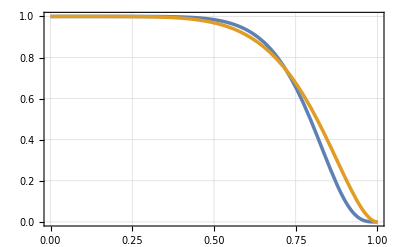

```mathematica
Clear[ϕ]
Plot[{%172,(1-λ^2) (1-Conjugate[λ]^2)+2 λ (1-λ^2) Conjugate[λ] (1-Conjugate[λ]^2)+3 λ^2 (1-λ^2) Conjugate[λ]^2 (1-Conjugate[λ]^2)+2 λ^3 (1-λ^2) Conjugate[λ]^3 (1-Conjugate[λ]^2)+λ^4 (1-λ^2) Conjugate[λ]^4 (1-Conjugate[λ]^2)},{λ,0,1}]
```

```mathematica
Conjugate[Exp[I]]*Exp[I]
```

1

```mathematica
FullSimplify[Refine[Cf[0,1,1,0,λ,ϕ]*Conjugate[Cf[0,1,1,0,λ,ϕ]],{Element[ϕ,Reals],Element[λ,Reals]}]]
Refine[FullSimplify[Pst[0,1,1,λ,ϕ]],{Element[ϕ,Reals],Element[λ,Reals]}]
```

λ^2 (-1+λ^2)^2 Cos[ϕ]^2

1/4 Abs[(1+ⅇ^(2 ⅈ ϕ)) λ (-1+λ^2)]^2

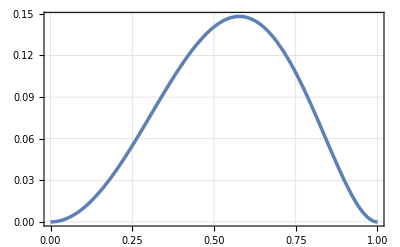

```mathematica
ϕt=Pi;
Plot[{λ^2 (-1+λ^2)^2 Cos[ϕt]^2},{λ,0,1}]
```

```mathematica
Sum[Pst[i,j,k,λ,Pi]*Pst[m,n,i+j-k,λ,Pi],{i,0,6},{j,0,6},{k,0,i+j},{m,0,6},{n,0,6}];
```

```mathematica
%176
```

Abs[1-λ^2]^4+2 Abs[1-λ^2]^2 Abs[λ (1-λ^2)]^2+2 Abs[λ (1-λ^2)]^4+2 Abs[1-λ^2]^2 Abs[λ^2 (1-λ^2)]^2+4 Abs[λ (1-λ^2)]^2 Abs[λ^2 (1-λ^2)]^2+3 Abs[λ^2 (1-λ^2)]^4+2 Abs[1-λ^2]^2 Abs[λ^3 (1-λ^2)]^2+4 Abs[λ (1-λ^2)]^2 Abs[λ^3 (1-λ^2)]^2+6 Abs[λ^2 (1-λ^2)]^2 Abs[λ^3 (1-λ^2)]^2+4 Abs[λ^3 (1-λ^2)]^4+2 Abs[λ (1-λ^2)]^2 Abs[λ^4 (1-λ^2)]^2+4 Abs[λ^2 (1-λ^2)]^2 Abs[λ^4 (1-λ^2)]^2+6 Abs[λ^3 (1-λ^2)]^2 Abs[λ^4 (1-λ^2)]^2+3 Abs[λ^4 (1-λ^2)]^4+2 Abs[λ^2 (1-λ^2)]^2 Abs[λ^5 (1-λ^2)]^2+4 Abs[λ^3 (1-λ^2)]^2 Abs[λ^5 (1-λ^2)]^2+4 Abs[λ^4 (1-λ^2)]^2 Abs[λ^5 (1-λ^2)]^2+2 Abs[λ^5 (1-λ^2)]^4+2 Abs[λ^3 (1-λ^2)]^2 Abs[λ^6 (1-λ^2)]^2+2 Abs[λ^4 (1-λ^2)]^2 Abs[λ^6 (1-λ^2)]^2+2 Abs[λ^5 (1-λ^2)]^2 Abs[λ^6 (1-λ^2)]^2+Abs[λ^6 (1-λ^2)]^4

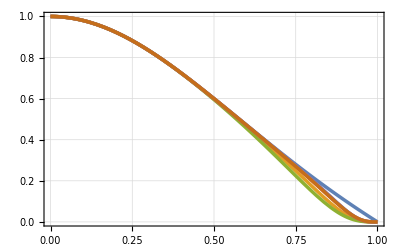

```mathematica
Plot[{(1-λ^2)/(1+λ^2),%181,%176,%183,%272,%277},{λ,0,1}]
```

```mathematica
Sum[Cf[i,a,b,j,λ,Pi/3]*Conjugate[Cf[i,A,B,j,λ,Pi/3]]*Cf[ip,A,B,jp,λ,Pi/3]*Conjugate[Cf[ip,a,b,jp,λ,Pi/2]],{i,0,5},{j,0,5},{A,0,5},{B,0,5},{a,0,5},{b,0,5},{ip,0,5},{jp,0,5}];
```

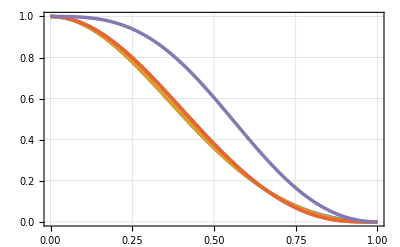

```mathematica
Plot[{((1-λ^2)/(1+λ^2))^2,%279,%282,%284,((1-λ^3)/(1+λ^3))^2},{λ,0,1}]
```

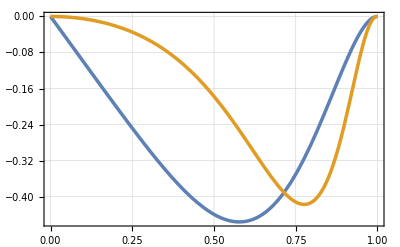

```mathematica
Plot[{-(1-λ^2)^2*(1+λ^2)^2*λ,((1-λ^2)^2*(1+λ^2)^2)-%284/((1-λ^2)/(1+λ^2))^2},{λ,0,1}]
```

```mathematica
{{
```